```mathematica
Dk[n_,k_,s_]:=Sum[j^-s Dk[n/j,k-1,s],{j,1,n}];Dk[n_,0,s_]:=UnitStep[n-1]
Table[Dk[n,k,0],{n,1,50},{k,1,7}]//TableForm
```

1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 3 | 4 | 5 | 6 | 7 | 8
3 | 5 | 7 | 9 | 11 | 13 | 15
4 | 8 | 13 | 19 | 26 | 34 | 43
5 | 10 | 16 | 23 | 31 | 40 | 50
6 | 14 | 25 | 39 | 56 | 76 | 99
7 | 16 | 28 | 43 | 61 | 82 | 106
8 | 20 | 38 | 63 | 96 | 138 | 190
9 | 23 | 44 | 73 | 111 | 159 | 218
10 | 27 | 53 | 89 | 136 | 195 | 267
11 | 29 | 56 | 93 | 141 | 201 | 274
12 | 35 | 74 | 133 | 216 | 327 | 470
13 | 37 | 77 | 137 | 221 | 333 | 477
14 | 41 | 86 | 153 | 246 | 369 | 526
15 | 45 | 95 | 169 | 271 | 405 | 575
16 | 50 | 110 | 204 | 341 | 531 | 785
17 | 52 | 113 | 208 | 346 | 537 | 792
18 | 58 | 131 | 248 | 421 | 663 | 988
19 | 60 | 134 | 252 | 426 | 669 | 995
20 | 66 | 152 | 292 | 501 | 795 | 1191
21 | 70 | 161 | 308 | 526 | 831 | 1240
22 | 74 | 170 | 324 | 551 | 867 | 1289
23 | 76 | 173 | 328 | 556 | 873 | 1296
24 | 84 | 203 | 408 | 731 | 1209 | 1884
25 | 87 | 209 | 418 | 746 | 1230 | 1912
26 | 91 | 218 | 434 | 771 | 1266 | 1961
27 | 95 | 228 | 454 | 806 | 1322 | 2045
28 | 101 | 246 | 494 | 881 | 1448 | 2241
29 | 103 | 249 | 498 | 886 | 1454 | 2248
30 | 111 | 276 | 562 | 1011 | 1670 | 2591
31 | 113 | 279 | 566 | 1016 | 1676 | 2598
32 | 119 | 300 | 622 | 1142 | 1928 | 3060
33 | 123 | 309 | 638 | 1167 | 1964 | 3109
34 | 127 | 318 | 654 | 1192 | 2000 | 3158
35 | 131 | 327 | 670 | 1217 | 2036 | 3207
36 | 140 | 363 | 770 | 1442 | 2477 | 3991
37 | 142 | 366 | 774 | 1447 | 2483 | 3998
38 | 146 | 375 | 790 | 1472 | 2519 | 4047
39 | 150 | 384 | 806 | 1497 | 2555 | 4096
40 | 158 | 414 | 886 | 1672 | 2891 | 4684
41 | 160 | 417 | 890 | 1677 | 2897 | 4691
42 | 168 | 444 | 954 | 1802 | 3113 | 5034
43 | 170 | 447 | 958 | 1807 | 3119 | 5041
44 | 176 | 465 | 998 | 1882 | 3245 | 5237
45 | 182 | 483 | 1038 | 1957 | 3371 | 5433
46 | 186 | 492 | 1054 | 1982 | 3407 | 5482
47 | 188 | 495 | 1058 | 1987 | 3413 | 5489
48 | 198 | 540 | 1198 | 2337 | 4169 | 6959
49 | 201 | 546 | 1208 | 2352 | 4190 | 6987
50 | 207 | 564 | 1248 | 2427 | 4316 | 7183

```mathematica
Dk[n_,k_,s_]:=Dk[n,k,s]=Sum[j^-s Dk[Floor[n/j],k-1,s],{j,1,n}];Dk[n_,0,s_]:=UnitStep[n-1]
Grid[Table[ Chop[ Dk[30000, k, s]-N[Zeta[s]^k]],{k,1,3},{s,2,4,.5}]]
```

-0.0000333328 | -1.28297×10^-7 | -5.55533×10^-10 | 0 | 0
-0.00041542 | -1.55614×10^-6 | -6.64545×10^-9 | 0 | 0
-0.00284113 | -0.0000103484 | -4.35834×10^-8 | -1.98172×10^-10 | 0

```mathematica
Dk1[n_,s_]:=Sum[j^-s,{j,1,n}]
Dk2[n_,s_]:=Sum[j^-s k^-s,{j,1,n},{k,1,n/j}]
Dk3[n_,s_]:=Sum[j^-s k^-s m^-s,{j,1,n},{k,1,n/j},{m,1,n/(j k)}]
Dk[n_,k_,s_]:=Sum[j^-s Dk[n/j,k-1,s],{j,1,n}];Dk[n_,0,s_]:=UnitStep[n-1]
FullSimplify[Table[{Dk1[n,s]-Dk[n,1,s],Dk2[n,s]-Dk[n,2,s],Dk3[n,s]-Dk[n,3,s]},{n,1,50}]//TableForm]
```

0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0

```mathematica
Dk2[5,s]
```

5+2^(1-s)+3^-s+4^-s+5^-s

```mathematica
Dk[5,2,s]
```

1+2^(1-2 s)+2^-s+2 3^-s+2 5^-s+2^-s (1+2^-s)

```mathematica
dk[n_,k_,s_]:=Sum[dk[j,1,s] dk[n/j,k-1,s],{j,Divisors[n]}];dk[n_, 1, s_] := n^-s ; dk[n_,0,s_]:=0;dk[1,0,s_]:=1
Dk[n_,k_,s_]:=Sum[j^-s Dk[n/j,k-1,s],{j,1,n}];Dk[n_,0,s_]:=UnitStep[n-1]
FullSimplify[Grid[Table[dk[n,k,s]-(Dk[n,k,s]-Dk[n-1,k,s]),{n,1,50,5},{k,1,5}]]]
```

0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0

```mathematica
Dmy[n_,k_,s_,y_]:=Sum[ (j+y)^-s Dmy[n(j+y)^-1,k-1,s,y],{j,1,n-y}];Dmy[n_,0,s_,y_]:=UnitStep[n-1]
Grid[Table[Chop[Dmy[30000,k,s,y]-N[Zeta[s,y+1]^k]],{k,1,3},{s,2,4},{y,1,4}]]
```

{-0.0000333328,-0.0000333328,-0.0000333328,-0.0000333328} | {-5.55537×10^-10,-5.55537×10^-10,-5.55537×10^-10,-5.55537×10^-10} | {0,0,0,0}
{-0.000348755,-0.000315423,-0.000293201,-0.000276536} | {-5.53439×10^-9,-4.97887×10^-9,-4.60854×10^-9,-4.3308×10^-9} | {0,0,0,0}
{-0.00169487,-0.00123141,-0.000963755,-0.000784785} | {-2.53136×10^-8,-1.8007×10^-8,-1.38248×10^-8,-1.1051×10^-8} | {0,0,0,0}

```mathematica
Dmy[1000,1,2,1]
```

999

```mathematica
Limit[ (n^z-n^0)z^-1,z->0]
```

Log[n]

```mathematica
Limit[ (n z^-1 +n^0)^z,z->Infinity]
```

ⅇ^n

```mathematica
Limit[ (n z +n^0)^(z^-1),z->0]
```

ⅇ^n

```mathematica
dz[n_,z_]:=dz[n,z]=Product[(-1)^p[[2]] Binomial[-z,p[[2]]],{p,FI[n]}];FI[n_]:=FactorInteger[n];FI[1]:={}
Dz[n_,z_]:=Dz[n,z]=Sum[dz[j,z],{j,1,n}]
bin[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
dd[ n_, k_, x_] := dd[n,k,x]=x Sum[ dd[ n (j x)^-1, k-1, x],{j,1,n x^-1}]; dd[n_, 0, x_] := UnitStep[n-1]
dda[n_, k_, x_] := x^k Dz[ Floor[n/(x^k)],k]
bd[n_, z_, x_] := Sum[ bin[z,k]dd[n,k,x],{k,0,Log[x,n]}]
bda[n_, z_, x_] := Sum[ bin[z,k]If[  bin[z,k] == 0, 0, dda[n,k,x]],{k,0,Log[x,n]}]
```

```mathematica
DiscretePlot[Expand[D[bda[n,z,1.05],z]]/.z->0,{n,2,20}]
```

```mathematica
dd[1527,4,4.3]
```

6495.72

```mathematica
dda[1527,4,4.3]
```

6495.72

```mathematica
DiscretePlot[bda[n,-1,1.1],{n,2,100}]
```

```mathematica
dd[1,1,1.00000001]
```

0.

```mathematica
bda[100,1,1.01]
```

100.99

```mathematica
D2[n_, k_] := D2[n,k]=Sum[ D2[Floor[n/j],k-1],{j,2,n}]; D2[n_, 0] := UnitStep[n-1]
```

```mathematica
D2a[n_, z_] := Sum[ Binomial[ z,k] D2[n,k],{k,0,Log[2,n]}]
D2b[n_, z_] := Sum[(-1)^k  Binomial[ z,k] D2[n,k],{k,0,Log[2,n]}]
```

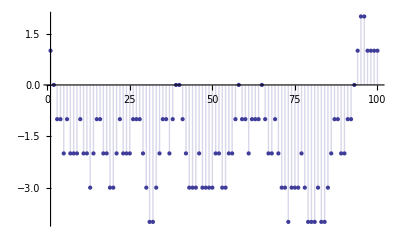

```mathematica
DiscretePlot[ D2a[n,-1],{n,1,100}]
```

```mathematica
D2a[1,2]
```

1

```mathematica
E2a[n_,k_, x_,s_]:= E2a[n,k,x,s]=Sum[ j^(-s)E2a[n/j,k-1,x,s],{j,2,n}]-x Sum[ (j x)^(-s)E2a[n/(x j),k-1,x,s],{j,1,n/x}];E2a[n_,0,a_,s_]:=UnitStep[n-1]
E2ab[n_,k_, x_,s_]:= E2ab[n,k,x,s]=Sum[ (j+1)^(-s)E2ab[n/(j+1),k-1,x,s]- x (j x)^(-s)E2ab[n/(x j),k-1,x,s],{j,1,n-1}];E2ab[n_,0,a_,s_]:=UnitStep[n-1]
E1a[n_,k_, x_,s_]:= E1a[n,k,x,s]=Sum[j^(-s) E1a[n/j,k-1,x,s],{j,1,n}]-x Sum[(j x)^(-s) E1a[n/(x j),k-1,x,s],{j,1,n/x}];E1a[n_,0,a_,s_]:=UnitStep[n-1]
E1ab[n_,k_, x_,s_]:= E1ab[n,k,x,s]=Sum[j^(-s) E1ab[n/j,k-1,x,s]-x (j x)^(-s) E1ab[n/(x j),k-1,x,s],{j,1,n}];E1ab[n_,0,a_,s_]:=UnitStep[n-1]
```

```mathematica
E1a[1,1,2,0]
```

1

```mathematica
E2a[1,1,2,0]
```

0

```mathematica
Series[ E^{x+1}^2,{x,0,10}]
```

{ⅇ+2 ⅇ x+3 ⅇ x^2+(10 ⅇ x^3)/3+(19 ⅇ x^4)/6+(13 ⅇ x^5)/5+(173 ⅇ x^6)/90+(407 ⅇ x^7)/315+(45 ⅇ x^8)/56+(5281 ⅇ x^9)/11340+(28787 ⅇ x^10)/113400+O[x]^11}

```mathematica
D2[n_, k_] := D2[n,k]=Sum[ D2[Floor[n/j],k-1],{j,2,n}]; D2[n_, 0] := UnitStep[n-1]
dz[n_,z_]:=dz[n,z]=Product[(-1)^p[[2]] Binomial[-z,p[[2]]],{p,FI[n]}];FI[n_]:=FactorInteger[n];FI[1]:={}
Dz[n_,z_]:=Dz[n,z]=Sum[dz[j,z],{j,1,n}]
F[n_, z_,t_] := Sum[ z^k/k! Dz[n,k],{k,0,t}]
F2[n_, z_] := Sum[ E^z z^k/k! D2[n,k],{k,0,Log[2,n]}]; F2[n_, 0] := UnitStep[n-1]
F3[n_, z_] := Sum[ z^k/k! D2[n,k],{k,0,Log[2,n]}]; F3[n_, 0] := UnitStep[n-1]
F33[n_, k_] := Sum[ (-1)^(k-j) Binomial[k,j] F3[n,j],{j,0,k}]
DF[n_] := Sum[ (-1)^(k+1)/k F33[n,k],{k,1,Log[2,n]}]
F33[n_,0] := UnitStep[n-1]
```

```mathematica
N[F[100,-1,30]]
```

-1.1951

```mathematica
N[F2[100,1]]
```

825.274

```mathematica
N[E^2 F3[100,2]]
```

9856.18

```mathematica
F33[100,7]
```

0

```mathematica
F2[100,2]
```

(12005 ⅇ^2)/9

```mathematica
DF[100]
```

99

```mathematica
Limit[ (n x^-1 + x^0)^x,x->Infinity]
```

ⅇ^n

```mathematica
L2[n_,1,b_]:=L2[n,1,b]=Sum[Log[j],{j,2,n}]-b Sum[Log[j b],{j,1,n/b}]
L2[n_,k_,b_]:=Sum[L2[n/j,k-1,b],{j,2,n}]-b Sum[L2[n/(j b),k-1,b],{j,1,n}]
E2a[n_,k_, x_,s_]:= E2a[n,k,x,s]=Sum[ j^(-s)E2a[n/j,k-1,x,s],{j,2,n}]-x Sum[ (j x)^(-s)E2a[n/(x j),k-1,x,s],{j,1,n/x}];E2a[n_,0,a_,s_]:=UnitStep[n-1]
```

```mathematica
{N[L2[20,1,2]],N[-D[E2a[20,1,2,s],s]/.s->0]}
```

{-1.73615,-1.73615}

```mathematica
{N[L2[20,2,2]],N[-D[E2a[20,2,2,s],s]/.s->0]/2}
```

{-1.77601,-1.77601}

```mathematica
{N[L2[20,3,2]],N[-D[E2a[20,3,2,s],s]/.s->0]/3}
```

{-0.875469,-0.875469}

```mathematica
f[n_, k_,s_,x_] := Sum[ j^-s ( k^-1 -f[n j^-1,k+1,s,x]),{j,2,n}] - x Sum[ (j x)^-s ( k^-1 -f[n (j x)^-1, k+1,s,x]), {j,1,n/x}]
```

```mathematica
N[D[f[100,1,s, 2],s]/.s->0]
```

-6.70877

```mathematica
D1y1[x_,s_,k_,y_]:=D1y1[x,s,k-1,y]+y Sum[(1+j y)^-s D1y1[x (1+j y)^-1,s,k-1,y],{j,1,(x-1)/y}];D1y1[x_,s_,0,y_]:=UnitStep[x-1]
D1y[x_,s_,k_,y_]:=y Sum[(1+j y)^-s D1y[x (1+j y)^-1,s,k-1,y],{j,1,(x-1)/y}];D1y[x_,s_,0,y_]:=UnitStep[x-1]
```

```mathematica
FullSimplify[y^(z(1-s)) Sum[ (j+y^-1)^-(z s),{j,1,Infinity}]/.{y->2, z->2, s->2}]
```

-4+π^4/24

```mathematica
Expand[(y^(1-s) Zeta[s, 1+y^-1])^z/.{y->2, z->2, s->2}]
```

4-π^2+π^4/16

```mathematica
Expand[(y^(z(1-s)) Zeta[s, 1+y^-1]^z)/.{y->2, z->2, s->2}]
```

4-π^2+π^4/16

```mathematica
Expand[(y^(z(1-s)) (Sum[ 1/(j + 1 + y^-1)^s,{j,0,Infinity}])^z)/.{y->2, z->2, s->2}]
```

4-π^2+π^4/16

```mathematica
Expand[(y^(z(1-s)) (Sum[(j + y^-1)^-s,{j,1,Infinity}])^z)/.{y->2, z->2, s->2}]
```

4-π^2+π^4/16

```mathematica
(j+y^-1)^-s (j+y^-1)^-s
```

(j+1/y)^(-2 s)

```mathematica
Expand[((1+y^-1)^-s+(2+y^-1)^-s+(3+y^-1)^-s+(4+y^-1)^-s+(5+y^-1)^-s)^2]
```

(1+1/y)^(-2 s)+(2+1/y)^(-2 s)+2 (1+1/y)^-s (2+1/y)^-s+(3+1/y)^(-2 s)+2 (1+1/y)^-s (3+1/y)^-s+2 (2+1/y)^-s (3+1/y)^-s+(4+1/y)^(-2 s)+2 (1+1/y)^-s (4+1/y)^-s+2 (2+1/y)^-s (4+1/y)^-s+2 (3+1/y)^-s (4+1/y)^-s+(5+1/y)^(-2 s)+2 (1+1/y)^-s (5+1/y)^-s+2 (2+1/y)^-s (5+1/y)^-s+2 (3+1/y)^-s (5+1/y)^-s+2 (4+1/y)^-s (5+1/y)^-s

```mathematica
D[ Sum[ (j+y^-1)^-s,{j,1,10}]^2,y]
```

2 ((1+1/y)^-s+(2+1/y)^-s+(3+1/y)^-s+(4+1/y)^-s+(5+1/y)^-s+(6+1/y)^-s+(7+1/y)^-s+(8+1/y)^-s+(9+1/y)^-s+(10+1/y)^-s) ((s (1+1/y)^(-1-s))/y^2+(s (2+1/y)^(-1-s))/y^2+(s (3+1/y)^(-1-s))/y^2+(s (4+1/y)^(-1-s))/y^2+(s (5+1/y)^(-1-s))/y^2+(s (6+1/y)^(-1-s))/y^2+(s (7+1/y)^(-1-s))/y^2+(s (8+1/y)^(-1-s))/y^2+(s (9+1/y)^(-1-s))/y^2+(s (10+1/y)^(-1-s))/y^2)

```mathematica
D[ y^(k(1-s))Sum[ (j+y^-1)^-s,{j,1,10}]^k,y]/.s->0
```

10^k k y^(-1+k)

```mathematica
D1[n_,z_,k_, s_]:=D1[n,z,k,s]=1+((z+1)/k-1) Sum[ j^-s D1[n/j,z,k+1,s],{j,2,n}]
Limit[ Limit[ D[D1[100,z,1,s],z],z->0],s->0]
-Limit[ D[N[Limit[ D[D1[100,z,1,s],z],z->0]],s],s->0]
```

428/15

94.0453

0

```mathematica
f1[n_, k_, s_] := Sum[ j^-s( k^-1 - f1[n/j,k+1,s]),{j,2,n}]
```

```mathematica
N[Limit[D[f1[100,1,s],s],s->0]]
```

-94.0453

```mathematica
s1[n_, k_, y_, s_] := s1[n,k,y,s]=y Sum[ (j y + 1)^-s( k^-1 - s1[ n (j y +1)^-1, k+1, y, s]),{j,1,(n-1)/y}]
```

```mathematica
-N[D[s1[100,1,.5,s],s]/.s->0]
```

95.6424

```mathematica
ml[ n_, k_] := Sum[ MoebiusMu[ d ] (Log[n/d])^k,{d, Divisors[n]}]
```

```mathematica
FullSimplify[ml[210,4]]
```

24 Log[2] Log[3] Log[5] Log[7]

```mathematica
dz[n_,z_, s_]:= n^-s Product[(-1)^p[[2]] Binomial[-z,p[[2]]],{p,FI[n]}];FI[n_]:=FactorInteger[n];FI[1]:={}
```

```mathematica
D[Limit[D[dz[210,z,s],{s,4}],s->0],{z}]
```

4 z^3 Log[210]^4

```mathematica
D[dz[2 3,z,0],{z,2}]/.z->0
```

2

```mathematica
dz[n_,z_,s_]:=dz[n,z,s]=If[n<1,0,n^-s Product[(-1)^p[[2]] Binomial[-z,p[[2]]],{p,FI[n]}]];FI[n_]:=FactorInteger[n];FI[1]:={}
Dz[n_,z_,s_]:=Dz[n,z,s]=Sum[dz[j,z,s],{j,1,n}]
```

```mathematica
Sum[ dz[j,1,-2] Dz[1000 j^-2, -1,-1],{j,1,1000^(1/2)}]
```

-1274

```mathematica
Sum[ dz[j,-1,-1] Dz[Floor[(1000/j)^(1/2)], 1,-2],{j,1,1000}]
```

-1274

```mathematica
Sum[ LiouvilleLambda[j] j^1,{j,1,1000}]
```

-1274

```mathematica
Sum[ dz[j,1,-1] Dz[Floor[(1000/j)^(1/2)], -1,-2],{j,1,1000}]
```

303076

```mathematica
Sum[MoebiusMu[j]^2 j^1,{j,1,1000}]
```

303076

```mathematica
FullSimplify[2^s / 3^(2 s)]
```

(2/9)^s

```mathematica
Expand[Sum[ MoebiusMu[n](n^-s) (m^(-2s)),{n,1,6},{m,1,6}]]
```

1-2^(-5 s)-2^(-3 s)+2^(-2 s)-2^-s-3^(-3 s)-2^(-2 s) 3^(-3 s)+2^-s 3^(-3 s)+3^(-2 s)-2^(-3 s) 3^(-2 s)-2^-s 3^(-2 s)-3^-s+2^(-5 s) 3^-s+2^(-3 s) 3^-s-2^(-2 s) 3^-s+4^(-2 s)-3^-s 4^(-2 s)-5^(-3 s)+5^(-2 s)-2^-s 5^(-2 s)-3^-s 5^(-2 s)-5^-s-2^(-2 s) 5^-s-3^(-2 s) 5^-s-4^(-2 s) 5^-s+6^(-3 s)+6^(-2 s)-5^-s 6^(-2 s)+6^-s+5^(-2 s) 6^-s

```mathematica
Table[ {n,MoebiusMu[n]},{n,1,20}]
```

{{1,1},{2,-1},{3,-1},{4,0},{5,-1},{6,1},{7,-1},{8,0},{9,0},{10,1},{11,-1},{12,0},{13,-1},{14,1},{15,1},{16,0},{17,-1},{18,0},{19,-1},{20,0}}

```mathematica
1/2^(2 s) (-1/2^s)
```

-2^(-3 s)

```mathematica
3^(2 s) 2^s
```

2^s 3^(2 s)

```mathematica
tt[n_]:=Sum[ If[ Floor[j^(1/2)] == j^(1/2),1,0] MoebiusMu[n/j],{j,Divisors[n]}]
```

```mathematica
Table[ Sum[ LiouvilleLambda[j],{j,Divisors[n]}],{n,1,30}]
```

{1,0,0,1,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0}

```mathematica
Table[tt[n]-LiouvilleLambda[n],{n,1,30}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Sum[ Floor[(300/j)^(1/2)]MoebiusMu[j],{j,1,300}]
```

-16

```mathematica
Sum[ LiouvilleLambda[ j ], {j,1,300}]
```

-16

```mathematica
Sum[ MoebiusMu[ n] x^n / (1-x^n),{n,1,Infinity}]
```

x

```mathematica
Sum[LiouvilleLambda[n] x^n / (1-x^n),{n,1,Infinity}]
```

∑_(n=1)^∞ (x^n LiouvilleLambda[n])/(1-x^n)

```mathematica
Table[ {n,Sum[ dz[j^2,2,0],{j,Divisors[n]}], dz[n,2,0]^2},{n,1,30}]
```

{{1,1,1},{2,4,4},{3,4,4},{4,9,9},{5,4,4},{6,16,16},{7,4,4},{8,16,16},{9,9,9},{10,16,16},{11,4,4},{12,36,36},{13,4,4},{14,16,16},{15,16,16},{16,25,25},{17,4,4},{18,36,36},{19,4,4},{20,36,36},{21,16,16},{22,16,16},{23,4,4},{24,64,64},{25,9,9},{26,16,16},{27,16,16},{28,36,36},{29,4,4},{30,64,64}}

```mathematica
Table[ {n,Sum[ MoebiusMu[n/j] dz[j,2,0]^2,{j,Divisors[n]}], dz[n^2,2,0]},{n,1,30}]
```

{{1,1,1},{2,3,3},{3,3,3},{4,5,5},{5,3,3},{6,9,9},{7,3,3},{8,7,7},{9,5,5},{10,9,9},{11,3,3},{12,15,15},{13,3,3},{14,9,9},{15,9,9},{16,9,9},{17,3,3},{18,15,15},{19,3,3},{20,15,15},{21,9,9},{22,9,9},{23,3,3},{24,21,21},{25,5,5},{26,9,9},{27,7,7},{28,15,15},{29,3,3},{30,27,27}}

```mathematica
Table[Sum[ dz[j^3,5,0],{j,Divisors[n]}],{n,1,30}]
```

{1,36,36,246,36,1296,36,961,246,1296,36,8856,36,1296,1296,2781,36,8856,36,8856,1296,1296,36,34596,246,1296,961,8856,36,46656}

```mathematica
bin[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
d2[n_, k_] := Sum[ d2[n/j, k-1], {j,2,n}]; d2[n_,0]:=UnitStep[n-1]
d2z[n_, z_] := Sum[ bin[z,k]d2[n,k],{k,0,Log[2,n]}]
dd2z[n_,z_]:= d2z[n,z]-d2z[n-1,z]
d3[n_, k_] := Sum[ d3[n/j, k-1], {j,3,n}]; d3[n_,0]:=UnitStep[n-1]
d3z[n_, z_] := Sum[ bin[z,k]d3[n,k],{k,0,Log[3,n]}]
dd3z[n_,z_]:= d3z[n,z]-d3z[n-1,z]
da[n_, k_,a_] := Sum[ da[n/(j+a), k-1,a], {j,1,n}]; da[n_,0,a_]:=UnitStep[n-1]
daz[n_, z_,a_] := Sum[ bin[z,k]da[n,k,a],{k,0,Log[a+1,n]}]
ddaz[n_,z_,a_]:= daz[n,z,a]-daz[n-1,z,a]
```

```mathematica
Expand[Table[ {n,(ddaz[n,z,1])} ,{n,2,100}]//TableForm]
```

2 | z
3 | z
4 | z+1/2 (-1+z) z
5 | z
6 | z+(-1+z) z
7 | z
8 | z+(-1+z) z+1/6 (-2+z) (-1+z) z
9 | z+1/2 (-1+z) z
10 | z+(-1+z) z
11 | z
12 | z+2 (-1+z) z+1/2 (-2+z) (-1+z) z
13 | z
14 | z+(-1+z) z
15 | z+(-1+z) z
16 | z+3/2 (-1+z) z+1/2 (-2+z) (-1+z) z+1/24 (-3+z) (-2+z) (-1+z) z
17 | z
18 | z+2 (-1+z) z+1/2 (-2+z) (-1+z) z
19 | z
20 | z+2 (-1+z) z+1/2 (-2+z) (-1+z) z
21 | z+(-1+z) z
22 | z+(-1+z) z
23 | z
24 | z+3 (-1+z) z+3/2 (-2+z) (-1+z) z+1/6 (-3+z) (-2+z) (-1+z) z
25 | z+1/2 (-1+z) z
26 | z+(-1+z) z
27 | z+(-1+z) z+1/6 (-2+z) (-1+z) z
28 | z+2 (-1+z) z+1/2 (-2+z) (-1+z) z
29 | z
30 | z+3 (-1+z) z+(-2+z) (-1+z) z
31 | z
32 | z+2 (-1+z) z+(-2+z) (-1+z) z+1/6 (-3+z) (-2+z) (-1+z) z+1/120 (-4+z) (-3+z) (-2+z) (-1+z) z
33 | z+(-1+z) z
34 | z+(-1+z) z
35 | z+(-1+z) z
36 | z+7/2 (-1+z) z+2 (-2+z) (-1+z) z+1/4 (-3+z) (-2+z) (-1+z) z
37 | z
38 | z+(-1+z) z
39 | z+(-1+z) z
40 | z+3 (-1+z) z+3/2 (-2+z) (-1+z) z+1/6 (-3+z) (-2+z) (-1+z) z
41 | z
42 | z+3 (-1+z) z+(-2+z) (-1+z) z
43 | z
44 | z+2 (-1+z) z+1/2 (-2+z) (-1+z) z
45 | z+2 (-1+z) z+1/2 (-2+z) (-1+z) z
46 | z+(-1+z) z
47 | z
48 | z+4 (-1+z) z+3 (-2+z) (-1+z) z+2/3 (-3+z) (-2+z) (-1+z) z+1/24 (-4+z) (-3+z) (-2+z) (-1+z) z
49 | z+1/2 (-1+z) z
50 | z+2 (-1+z) z+1/2 (-2+z) (-1+z) z
51 | z+(-1+z) z
52 | z+2 (-1+z) z+1/2 (-2+z) (-1+z) z
53 | z
54 | z+3 (-1+z) z+3/2 (-2+z) (-1+z) z+1/6 (-3+z) (-2+z) (-1+z) z
55 | z+(-1+z) z
56 | z+3 (-1+z) z+3/2 (-2+z) (-1+z) z+1/6 (-3+z) (-2+z) (-1+z) z
57 | z+(-1+z) z
58 | z+(-1+z) z
59 | z
60 | z+5 (-1+z) z+7/2 (-2+z) (-1+z) z+1/2 (-3+z) (-2+z) (-1+z) z
61 | z
62 | z+(-1+z) z
63 | z+2 (-1+z) z+1/2 (-2+z) (-1+z) z
64 | z+5/2 (-1+z) z+5/3 (-2+z) (-1+z) z+5/12 (-3+z) (-2+z) (-1+z) z+1/24 (-4+z) (-3+z) (-2+z) (-1+z) z+1/720 (-5+z) (-4+z) (-3+z) (-2+z) (-1+z) z
65 | z+(-1+z) z
66 | z+3 (-1+z) z+(-2+z) (-1+z) z
67 | z
68 | z+2 (-1+z) z+1/2 (-2+z) (-1+z) z
69 | z+(-1+z) z
70 | z+3 (-1+z) z+(-2+z) (-1+z) z
71 | z
72 | z+5 (-1+z) z+9/2 (-2+z) (-1+z) z+7/6 (-3+z) (-2+z) (-1+z) z+1/12 (-4+z) (-3+z) (-2+z) (-1+z) z
73 | z
74 | z+(-1+z) z
75 | z+2 (-1+z) z+1/2 (-2+z) (-1+z) z
76 | z+2 (-1+z) z+1/2 (-2+z) (-1+z) z
77 | z+(-1+z) z
78 | z+3 (-1+z) z+(-2+z) (-1+z) z
79 | z
80 | z+4 (-1+z) z+3 (-2+z) (-1+z) z+2/3 (-3+z) (-2+z) (-1+z) z+1/24 (-4+z) (-3+z) (-2+z) (-1+z) z
81 | z+3/2 (-1+z) z+1/2 (-2+z) (-1+z) z+1/24 (-3+z) (-2+z) (-1+z) z
82 | z+(-1+z) z
83 | z
84 | z+5 (-1+z) z+7/2 (-2+z) (-1+z) z+1/2 (-3+z) (-2+z) (-1+z) z
85 | z+(-1+z) z
86 | z+(-1+z) z
87 | z+(-1+z) z
88 | z+3 (-1+z) z+3/2 (-2+z) (-1+z) z+1/6 (-3+z) (-2+z) (-1+z) z
89 | z
90 | z+5 (-1+z) z+7/2 (-2+z) (-1+z) z+1/2 (-3+z) (-2+z) (-1+z) z
91 | z+(-1+z) z
92 | z+2 (-1+z) z+1/2 (-2+z) (-1+z) z
93 | z+(-1+z) z
94 | z+(-1+z) z
95 | z+(-1+z) z
96 | z+5 (-1+z) z+5 (-2+z) (-1+z) z+5/3 (-3+z) (-2+z) (-1+z) z+5/24 (-4+z) (-3+z) (-2+z) (-1+z) z+1/120 (-5+z) (-4+z) (-3+z) (-2+z) (-1+z) z
97 | z
98 | z+2 (-1+z) z+1/2 (-2+z) (-1+z) z
99 | z+2 (-1+z) z+1/2 (-2+z) (-1+z) z
100 | z+7/2 (-1+z) z+2 (-2+z) (-1+z) z+1/4 (-3+z) (-2+z) (-1+z) z

```mathematica
bin[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
E2a[n_,k_, x_,s_]:= E2a[n,k,x,s]=Sum[ j^(-s)E2a[n/j,k-1,x,s],{j,2,n}]-x Sum[ (j x)^(-s)E2a[n/(x j),k-1,x,s],{j,1,n/x}];E2a[n_,0,a_,s_]:=UnitStep[n-1]
E1[n_,z_,x_,s_]:=E1[n,z,x,s]=Sum[ bin[z,k] E2a[n,k,x,s],{k,0,Log[If[x<2,x,2],n]}]
e1[n_, z_, x_, s_] := E1[n,z,x,s]-E1[n-1,z,x,s]
```

```mathematica
Expand[e1[100,z,2,0]]
```

-(3 z^2)/4-z^3/2+z^4/4

```mathematica
Expand[e1[100,z,1.05,0]]
```

0.-9.77707×10^-11 z-1.34015 z^2+3.89813 z^3-7.32015 z^4+9.36244 z^5-8.6053 z^6+6.55789 z^7-4.04874 z^8+2.12208 z^9-0.943584 z^10+0.35776 z^11-0.116825 z^12+0.0332317 z^13-0.00832691 z^14+0.00185612 z^15-0.000371057 z^16+0.0000669551 z^17-0.0000109615 z^18+1.63515×10^-6 z^19-2.23076×10^-7 z^20+2.79247×10^-8 z^21-3.21707×10^-9 z^22+3.42029×10^-10 z^23-3.36434×10^-11 z^24+3.06896×10^-12 z^25-2.60182×10^-13 z^26+2.05409×10^-14 z^27-1.51286×10^-15 z^28+1.04118×10^-16 z^29-6.70546×10^-18 z^30+4.04648×10^-19 z^31-2.29074×10^-20 z^32+1.21779×10^-21 z^33-6.08504×10^-23 z^34+2.86024×10^-24 z^35-1.2656×10^-25 z^36+5.27494×10^-27 z^37-2.07205×10^-28 z^38+7.67436×10^-30 z^39-2.6811×10^-31 z^40+8.83783×10^-33 z^41-2.74945×10^-34 z^42+8.07395×10^-36 z^43-2.23826×10^-37 z^44+5.85776×10^-39 z^45-1.44721×10^-40 z^46+3.37492×10^-42 z^47-7.42757×10^-44 z^48+1.5423×10^-45 z^49-3.02052×10^-47 z^50+5.57704×10^-49 z^51-9.70324×10^-51 z^52+1.58987×10^-52 z^53-2.45152×10^-54 z^54+3.55461×10^-56 z^55-4.84212×10^-58 z^56+6.19036×10^-60 z^57-7.41862×10^-62 z^58+8.32305×10^-64 z^59-8.72862×10^-66 z^60+8.54243×10^-68 z^61-7.78695×10^-70 z^62+6.59739×10^-72 z^63-5.18256×10^-74 z^64+3.76433×10^-76 z^65-2.52024×10^-78 z^66+1.54968×10^-80 z^67-8.71547×10^-83 z^68+4.46166×10^-85 z^69-2.06732×10^-87 z^70+8.61236×10^-90 z^71-3.20003×10^-92 z^72+1.05016×10^-94 z^73-3.0071×10^-97 z^74+7.3977×10^-100 z^75-1.532×10^-102 z^76+2.59716×10^-105 z^77-3.46094×10^-108 z^78+3.3995×10^-111 z^79-2.18828×10^-114 z^80+6.92494×10^-118 z^81

```mathematica
ff[n_] :=(Sign[Abs[n]-1]+1)/2
```

```mathematica
fp[k_] :=Sum[ Binomial[k,j] BernoulliB[k-j]/(j+1) n^(j+1),{j,0,k}]
```

```mathematica
FullSimplify[fp[3]]
```

1/4 (-1+n)^2 n^2

```mathematica
fa[n_,a_] := N[(Sin[n]+(3 n-3)^(1/2)-1)Sum[ BernoulliB[k]/k! D[ ((Sin[n]+(3n-3)^(1/2))^z), {z, k+a-1}]/.z->0,{k,0,200}]]
```

```mathematica
fa[100,3]
```

22.3553

```mathematica
bin[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
D2[n_, k_, s_] := D2[n,k,s]=Sum[ j^-s D2[Floor[n/j], k-1,s],{j,2,n}];D2[n_,0,s_]:=1
Dz[n_, z_, s_] := Sum [ bin[ z,k] D2[n,k,s],{k,0,Log[2,n]}]
```

```mathematica
1+Integrate[ D[Dz[100,z,0],z],{z,0,1}]
```

100

```mathematica
Dz[100,3,0]
```

1471

```mathematica
Expand[D[Dz[100,z,0],z]]
```

428/15+(16289 z)/180+(993 z^2)/16+(611 z^3)/36+(67 z^4)/48+(7 z^5)/120

```mathematica
FullSimplify[D[Dz[100,z,s],z]/.z->0]
```

1/3 2^(-1-6 s)+2^(-1-2 s)+2^(-5 s)/5+2^(-3 s)/3+2^-s+3^(-1-3 s)+3^(-4 s)/4+3^(-2 s)/2+3^-s+4^(-1-2 s)+5^(-2 s)/2+5^-s+7^(-2 s)/2+7^-s+11^-s+13^-s+17^-s+19^-s+23^-s+29^-s+31^-s+37^-s+41^-s+43^-s+47^-s+53^-s+59^-s+61^-s+67^-s+71^-s+73^-s+79^-s+83^-s+89^-s+97^-s

```mathematica
0-Integrate[ D[1/3 2^(-1-6 s)+2^(-1-2 s)+2^(-5 s)/5+2^(-3 s)/3+2^-s+3^(-1-3 s)+3^(-4 s)/4+3^(-2 s)/2+3^-s+4^(-1-2 s)+5^(-2 s)/2+5^-s+7^(-2 s)/2+7^-s+11^-s+13^-s+17^-s+19^-s+23^-s+29^-s+31^-s+37^-s+41^-s+43^-s+47^-s+53^-s+59^-s+61^-s+67^-s+71^-s+73^-s+79^-s+83^-s+89^-s+97^-s,s],{s,0,Infinity}]
```

428/15

```mathematica
Dz[100,2,-1]
```

26879

```mathematica
1-Expand[Integrate[ D[Dz[10,z,s],s],{s,0,Infinity}]]
```

Integrate::idiv: Integral of -2^s\ z\ Log[2] + 2^2\ s\ z\ Log[2] - 2^3\ s\ z\ Log[2] + 2^-1 + 3\ s\ z\ Log[2] + 2^-1 + s\ 5^s\ z\ Log[2] + 6^s\ z\ Log[2] - 2^2\ s\ z^2\ Log[2] + 2^3\ s\ z^2\ Log[2] - 2^-1 + s\ 5^s\ z^2\ Log[2] - 6^s\ z^2\ Log[2] - 2^-1 + 3\ s\ z^3\ Log[2] - 3^s\ z\ Log[3] + 3^2\ s\ z\ Log[3] + 6^s\ z\ Log[3] - 3^2\ s\ z^2\ Log[3] - 6^s\ z^2\ Log[3] + 2^-1 + 3\ s\ z\ Log[4] - 4^s\ z\ Log[4] - 2^-1 + 3\ s\ z^2\ Log[4] - 5^s\ z\ Log[5] + 2^-1 + s\ 5^s\ z\ Log[5] - 2^-1 + s\ 5^s\ z^2\ Log[5] - 6^s\ z\ Log[6] - 7^s\ z\ Log[7] + 2^-1 + 3\ s\ z\ Log[8] - 8^s\ z\ Log[8] - 2^-1 + 3\ s\ z^2\ Log[8] - 9^s\ z\ Log[9] + 2^-1 + s\ 5^s\ z\ Log[10] - 10^s\ z\ Log[10] - 2^-1 + s\ 5^s\ z^2\ Log[10] does not converge on {0, ∞}.

1-∫_0^(-∞) (-2^(-1-3 s) (-2+z) (-1+z) z Log[2]+1/2 (-1+z) z (-2^-s (2^-s+3^-s+4^-s+5^-s) Log[2]-3^-s (2^-s+3^-s) Log[3]+3^-s (-2^-s Log[2]-3^-s Log[3])+2^-s (-2^-s Log[2]-3^-s Log[3]-4^-s Log[4]-5^-s Log[5])-8^-s Log[8]-10^-s Log[10])+z (-2^-s Log[2]-3^-s Log[3]-4^-s Log[4]-5^-s Log[5]-6^-s Log[6]-7^-s Log[7]-8^-s Log[8]-9^-s Log[9]-10^-s Log[10]))ⅆs

```mathematica
Expand[Dz[10,z,-1]]
```

1+(157 z)/6+(53 z^2)/2+(4 z^3)/3

```mathematica
Expand[FullSimplify[1-Expand[Integrate[ D[Dz[10,z,s],s],{s,-1,Infinity}]]]]
```

1+(157 z)/6+(53 z^2)/2+(4 z^3)/3

```mathematica
D[n^z,z]
```

```mathematica
FullSimplify[Integrate[ n^z Log[n],{z,1,2}]]
```

(-1+n) n

```mathematica
FullSimplify[Integrate[ n^z Log[n],{z,3,2}]]
```

-(-1+n) n^2

```mathematica
Integrate[ D[ fn[x],x],{x,0,100}]
```

-fn[0]+fn[100]

```mathematica
{Limit[y^(s-1) HurwitzZeta[s,y+1],y->Infinity],1/(s-1)}
```

{1/(-1+s),1/(-1+s)}

```mathematica
bin[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
D2[n_, k_, s_] := D2[n,k,s]=Sum[ j^-s D2[Floor[n/j], k-1,s],{j,2,n}];D2[n_,0,s_]:=1
Dz[n_, z_, s_] := Sum [ bin[ z,k] D2[n,k,s],{k,0,Log[2,n]}]
sind[ n_, z_, s_, t_] := Sum[ z^k (D[Sin[x],{x,k}]/.x->0)/k! Dz[ n, k,s],{k,0,t}]
cosd[ n_, z_, s_, t_] := Sum[ z^k (D[Cos[x],{x,k}]/.x->0)/k! Dz[ n, k,s],{k,0,t}]
```

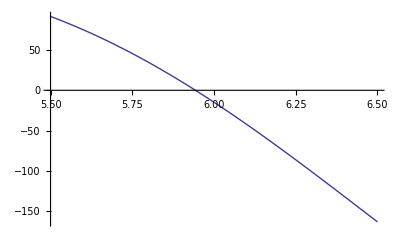

```mathematica
Plot[ N[sind[ 12, s, 0, 80]],{s,5.5,6.5}]
```

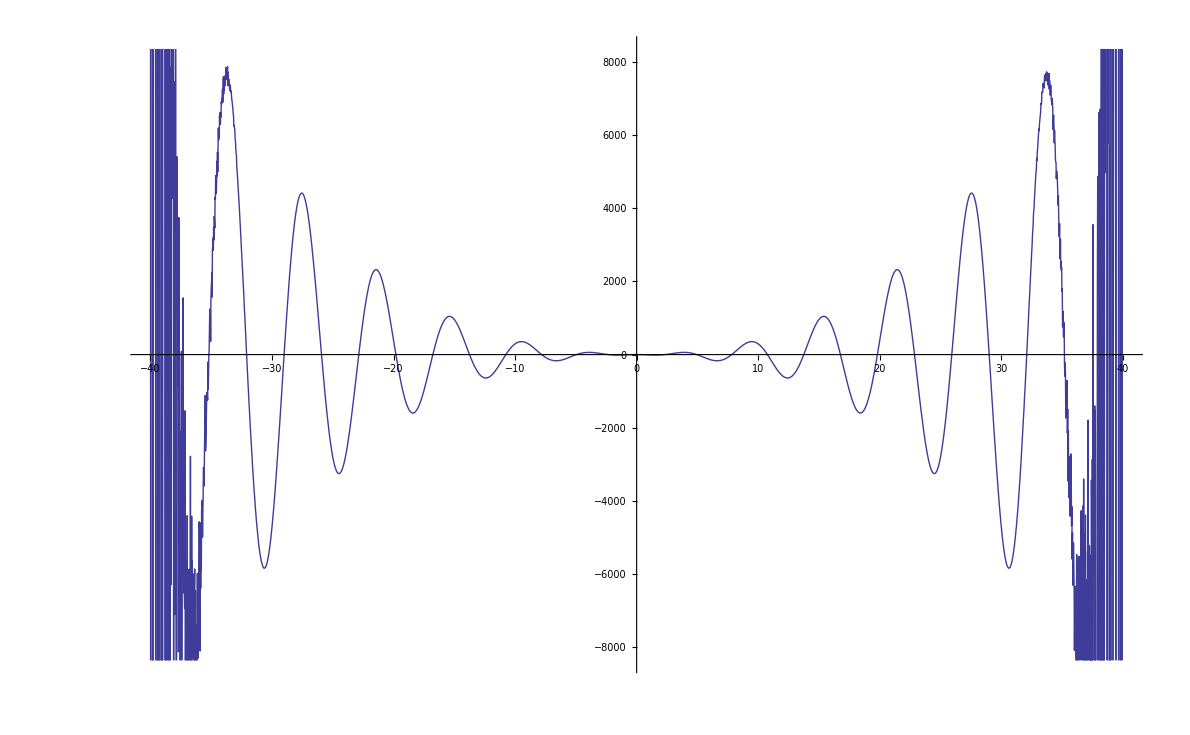

```mathematica
Plot[ N[cosd[ 10, s, 0, 200]],{s,-40,40}]
```

```mathematica
sind[10,N[2 Pi],0,90]
```

15.207

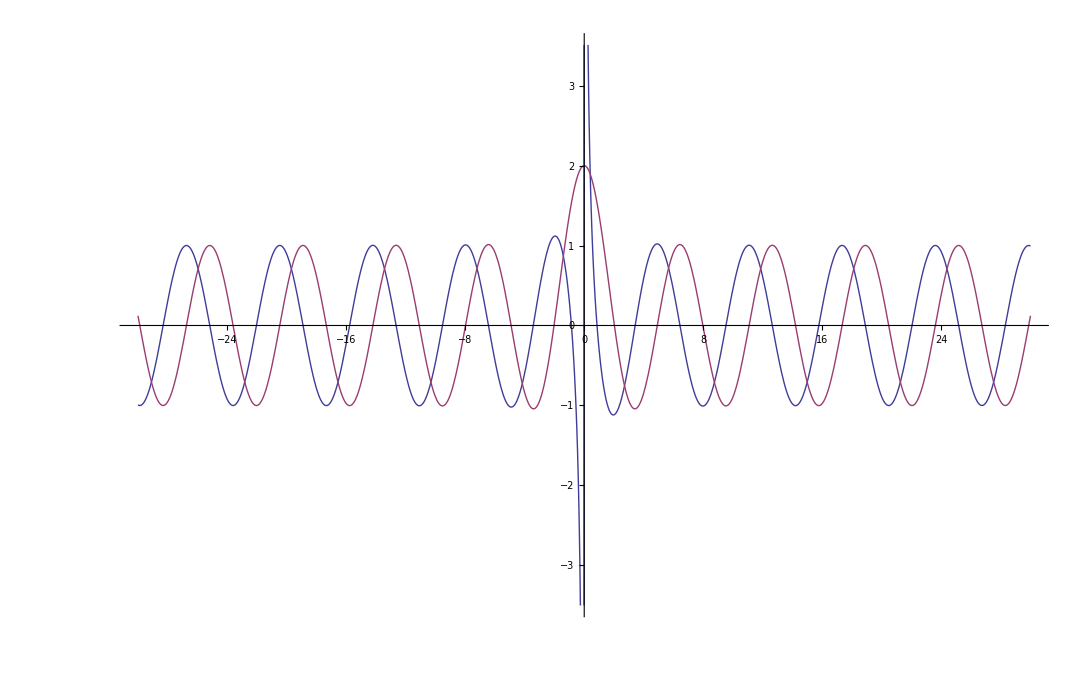

```mathematica
Plot[ {N[cosd[ E, s, 0, 200]]/s, N[sind[ E, s, 0, 200]]/s},{s,-30,30}]
```

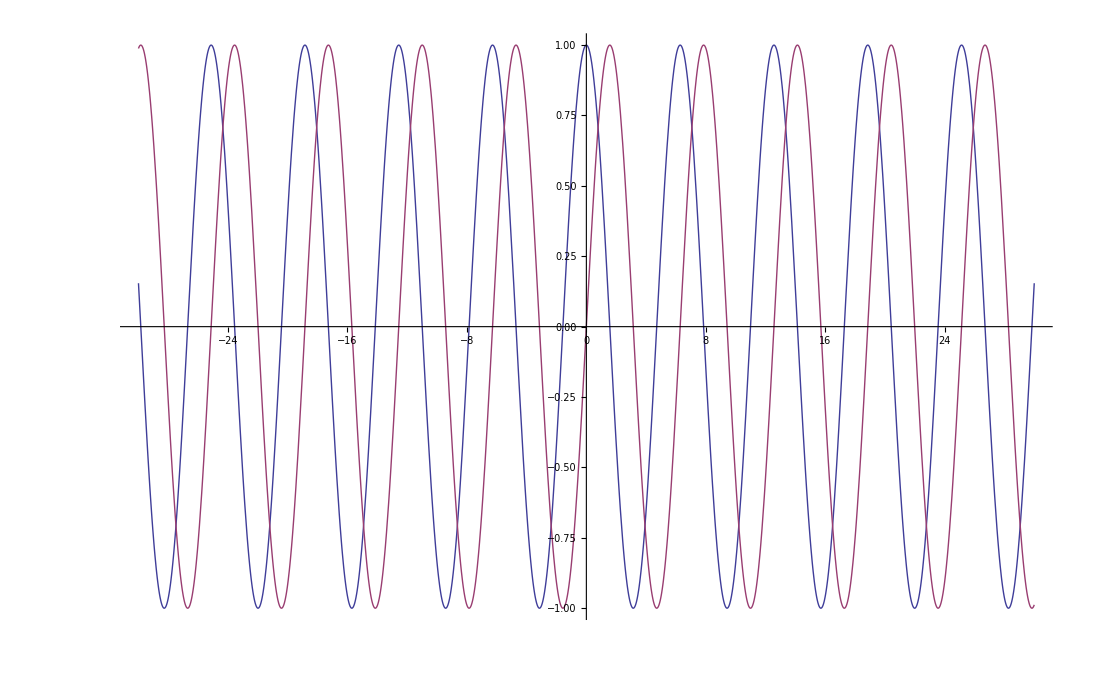

```mathematica
Plot[ {Cos[s],Sin[s]},{s,-30,30}]
```

```mathematica
Table[ {s,N[cosd[ E, s, 0, 400]]/s},{s,4,18, .01}]//TableForm
```

4. | 0.593392
4.01 | 0.602193
4.02 | 0.610923
4.03 | 0.61958
4.04 | 0.628163
4.05 | 0.636673
4.06 | 0.645107
4.07 | 0.653465
4.08 | 0.661747
4.09 | 0.669951
4.1 | 0.678076
4.11 | 0.686122
4.12 | 0.694089
4.13 | 0.701974
4.14 | 0.709778
4.15 | 0.7175
4.16 | 0.725138
4.17 | 0.732693
4.18 | 0.740163
4.19 | 0.747548
4.2 | 0.754847
4.21 | 0.762059
4.22 | 0.769184
4.23 | 0.776221
4.24 | 0.783169
4.25 | 0.790028
4.26 | 0.796796
4.27 | 0.803474
4.28 | 0.81006
4.29 | 0.816555
4.3 | 0.822957
4.31 | 0.829265
4.32 | 0.83548
4.33 | 0.841601
4.34 | 0.847626
4.35 | 0.853556
4.36 | 0.85939
4.37 | 0.865127
4.38 | 0.870767
4.39 | 0.87631
4.4 | 0.881754
4.41 | 0.887099
4.42 | 0.892345
4.43 | 0.897492
4.44 | 0.902538
4.45 | 0.907484
4.46 | 0.912328
4.47 | 0.917071
4.48 | 0.921712
4.49 | 0.926251
4.5 | 0.930687
4.51 | 0.935019
4.52 | 0.939248
4.53 | 0.943374
4.54 | 0.947394
4.55 | 0.951311
4.56 | 0.955122
4.57 | 0.958828
4.58 | 0.962428
4.59 | 0.965922
4.6 | 0.96931
4.61 | 0.972591
4.62 | 0.975766
4.63 | 0.978833
4.64 | 0.981794
4.65 | 0.984646
4.66 | 0.987391
4.67 | 0.990028
4.68 | 0.992556
4.69 | 0.994976
4.7 | 0.997287
4.71 | 0.99949
4.72 | 1.00158
4.73 | 1.00357
4.74 | 1.00544
4.75 | 1.00721
4.76 | 1.00887
4.77 | 1.01041
4.78 | 1.01185
4.79 | 1.01318
4.8 | 1.01439
4.81 | 1.0155
4.82 | 1.0165
4.83 | 1.01739
4.84 | 1.01816
4.85 | 1.01883
4.86 | 1.01939
4.87 | 1.01983
4.88 | 1.02017
4.89 | 1.0204
4.9 | 1.02052
4.91 | 1.02052
4.92 | 1.02042
4.93 | 1.02021
4.94 | 1.01989
4.95 | 1.01945
4.96 | 1.01891
4.97 | 1.01826
4.98 | 1.0175
4.99 | 1.01663
5. | 1.01566
5.01 | 1.01457
5.02 | 1.01337
5.03 | 1.01207
5.04 | 1.01066
5.05 | 1.00914
5.06 | 1.00751
5.07 | 1.00578
5.08 | 1.00393
5.09 | 1.00198
5.1 | 0.999928
5.11 | 0.997765
5.12 | 0.995496
5.13 | 0.99312
5.14 | 0.99064
5.15 | 0.988053
5.16 | 0.985362
5.17 | 0.982566
5.18 | 0.979666
5.19 | 0.976662
5.2 | 0.973554
5.21 | 0.970343
5.22 | 0.967029
5.23 | 0.963613
5.24 | 0.960095
5.25 | 0.956475
5.26 | 0.952753
5.27 | 0.948932
5.28 | 0.94501
5.29 | 0.940988
5.3 | 0.936866
5.31 | 0.932646
5.32 | 0.928328
5.33 | 0.923911
5.34 | 0.919398
5.35 | 0.914787
5.36 | 0.91008
5.37 | 0.905277
5.38 | 0.900379
5.39 | 0.895387
5.4 | 0.8903
5.41 | 0.88512
5.42 | 0.879847
5.43 | 0.874481
5.44 | 0.869024
5.45 | 0.863476
5.46 | 0.857837
5.47 | 0.852108
5.48 | 0.84629
5.49 | 0.840384
5.5 | 0.834389
5.51 | 0.828308
5.52 | 0.822139
5.53 | 0.815885
5.54 | 0.809546
5.55 | 0.803122
5.56 | 0.796614
5.57 | 0.790024
5.58 | 0.783351
5.59 | 0.776596
5.6 | 0.769761
5.61 | 0.762845
5.62 | 0.75585
5.63 | 0.748776
5.64 | 0.741625
5.65 | 0.734396
5.66 | 0.727092
5.67 | 0.719712
5.68 | 0.712257
5.69 | 0.704728
5.7 | 0.697126
5.71 | 0.689452
5.72 | 0.681707
5.73 | 0.673891
5.74 | 0.666006
5.75 | 0.658052
5.76 | 0.650029
5.77 | 0.64194
5.78 | 0.633784
5.79 | 0.625563
5.8 | 0.617278
5.81 | 0.608929
5.82 | 0.600517
5.83 | 0.592044
5.84 | 0.583509
5.85 | 0.574915
5.86 | 0.566262
5.87 | 0.55755
5.88 | 0.548782
5.89 | 0.539957
5.9 | 0.531076
5.91 | 0.522142
5.92 | 0.513154
5.93 | 0.504114
5.94 | 0.495022
5.95 | 0.485879
5.96 | 0.476687
5.97 | 0.467447
5.98 | 0.458159
5.99 | 0.448824
6. | 0.439444
6.01 | 0.430019
6.02 | 0.420551
6.03 | 0.411039
6.04 | 0.401487
6.05 | 0.391894
6.06 | 0.382261
6.07 | 0.372589
6.08 | 0.36288
6.09 | 0.353135
6.1 | 0.343354
6.11 | 0.333539
6.12 | 0.32369
6.13 | 0.313809
6.14 | 0.303896
6.15 | 0.293954
6.16 | 0.283982
6.17 | 0.273981
6.18 | 0.263954
6.19 | 0.2539
6.2 | 0.243822
6.21 | 0.23372
6.22 | 0.223594
6.23 | 0.213447
6.24 | 0.203279
6.25 | 0.193091
6.26 | 0.182885
6.27 | 0.172661
6.28 | 0.16242
6.29 | 0.152164
6.3 | 0.141894
6.31 | 0.13161
6.32 | 0.121314
6.33 | 0.111007
6.34 | 0.10069
6.35 | 0.0903639
6.36 | 0.0800299
6.37 | 0.069689
6.38 | 0.0593423
6.39 | 0.0489909
6.4 | 0.0386359
6.41 | 0.0282784
6.42 | 0.0179194
6.43 | 0.00756007
6.44 | -0.0027986
6.45 | -0.0131555
6.46 | -0.0235095
6.47 | -0.0338597
6.48 | -0.0442048
6.49 | -0.0545438
6.5 | -0.0648757
6.51 | -0.0751994
6.52 | -0.0855138
6.53 | -0.0958179
6.54 | -0.10611
6.55 | -0.116391
6.56 | -0.126657
6.57 | -0.136909
6.58 | -0.147145
6.59 | -0.157365
6.6 | -0.167567
6.61 | -0.17775
6.62 | -0.187913
6.63 | -0.198055
6.64 | -0.208175
6.65 | -0.218272
6.66 | -0.228345
6.67 | -0.238392
6.68 | -0.248414
6.69 | -0.258409
6.7 | -0.268375
6.71 | -0.278312
6.72 | -0.288219
6.73 | -0.298094
6.74 | -0.307937
6.75 | -0.317747
6.76 | -0.327522
6.77 | -0.337262
6.78 | -0.346966
6.79 | -0.356633
6.8 | -0.366261
6.81 | -0.37585
6.82 | -0.385398
6.83 | -0.394905
6.84 | -0.40437
6.85 | -0.413792
6.86 | -0.42317
6.87 | -0.432502
6.88 | -0.441788
6.89 | -0.451028
6.9 | -0.460219
6.91 | -0.469361
6.92 | -0.478453
6.93 | -0.487495
6.94 | -0.496485
6.95 | -0.505422
6.96 | -0.514306
6.97 | -0.523135
6.98 | -0.531908
6.99 | -0.540626
7. | -0.549286
7.01 | -0.557889
7.02 | -0.566432
7.03 | -0.574915
7.04 | -0.583338
7.05 | -0.5917
7.06 | -0.599999
7.07 | -0.608234
7.08 | -0.616406
7.09 | -0.624513
7.1 | -0.632554
7.11 | -0.640529
7.12 | -0.648436
7.13 | -0.656275
7.14 | -0.664045
7.15 | -0.671746
7.16 | -0.679375
7.17 | -0.686934
7.18 | -0.694421
7.19 | -0.701834
7.2 | -0.709175
7.21 | -0.716441
7.22 | -0.723631
7.23 | -0.730746
7.24 | -0.737785
7.25 | -0.744747
7.26 | -0.75163
7.27 | -0.758435
7.28 | -0.765161
7.29 | -0.771806
7.3 | -0.778371
7.31 | -0.784855
7.32 | -0.791257
7.33 | -0.797576
7.34 | -0.803812
7.35 | -0.809964
7.36 | -0.816031
7.37 | -0.822014
7.38 | -0.827911
7.39 | -0.833721
7.4 | -0.839445
7.41 | -0.845081
7.42 | -0.850629
7.43 | -0.856089
7.44 | -0.86146
7.45 | -0.86674
7.46 | -0.871931
7.47 | -0.877031
7.48 | -0.88204
7.49 | -0.886957
7.5 | -0.891782
7.51 | -0.896514
7.52 | -0.901153
7.53 | -0.905699
7.54 | -0.91015
7.55 | -0.914507
7.56 | -0.918769
7.57 | -0.922936
7.58 | -0.927006
7.59 | -0.930981
7.6 | -0.934859
7.61 | -0.93864
7.62 | -0.942324
7.63 | -0.94591
7.64 | -0.949398
7.65 | -0.952788
7.66 | -0.956079
7.67 | -0.959271
7.68 | -0.962364
7.69 | -0.965357
7.7 | -0.96825
7.71 | -0.971042
7.72 | -0.973735
7.73 | -0.976326
7.74 | -0.978817
7.75 | -0.981206
7.76 | -0.983494
7.77 | -0.98568
7.78 | -0.987764
7.79 | -0.989746
7.8 | -0.991626
7.81 | -0.993403
7.82 | -0.995078
7.83 | -0.99665
7.84 | -0.998119
7.85 | -0.999485
7.86 | -1.00075
7.87 | -1.00191
7.88 | -1.00296
7.89 | -1.00392
7.9 | -1.00476
7.91 | -1.00551
7.92 | -1.00615
7.93 | -1.00669
7.94 | -1.00712
7.95 | -1.00745
7.96 | -1.00768
7.97 | -1.0078
7.98 | -1.00782
7.99 | -1.00773
8. | -1.00755
8.01 | -1.00725
8.02 | -1.00686
8.03 | -1.00636
8.04 | -1.00575
8.05 | -1.00504
8.06 | -1.00423
8.07 | -1.00332
8.08 | -1.0023
8.09 | -1.00118
8.1 | -0.999957
8.11 | -0.99863
8.12 | -0.997201
8.13 | -0.995669
8.14 | -0.994035
8.15 | -0.992299
8.16 | -0.99046
8.17 | -0.98852
8.18 | -0.986478
8.19 | -0.984335
8.2 | -0.982091
8.21 | -0.979746
8.22 | -0.9773
8.23 | -0.974754
8.24 | -0.972108
8.25 | -0.969362
8.26 | -0.966516
8.27 | -0.963571
8.28 | -0.960528
8.29 | -0.957385
8.3 | -0.954145
8.31 | -0.950807
8.32 | -0.947371
8.33 | -0.943838
8.34 | -0.940208
8.35 | -0.936482
8.36 | -0.93266
8.37 | -0.928742
8.38 | -0.924729
8.39 | -0.920621
8.4 | -0.916419
8.41 | -0.912123
8.42 | -0.907734
8.43 | -0.903251
8.44 | -0.898676
8.45 | -0.894009
8.46 | -0.889251
8.47 | -0.884402
8.48 | -0.879462
8.49 | -0.874432
8.5 | -0.869312
8.51 | -0.864104
8.52 | -0.858807
8.53 | -0.853422
8.54 | -0.84795
8.55 | -0.842391
8.56 | -0.836747
8.57 | -0.831016
8.58 | -0.825201
8.59 | -0.819301
8.6 | -0.813318
8.61 | -0.807252
8.62 | -0.801103
8.63 | -0.794872
8.64 | -0.78856
8.65 | -0.782167
8.66 | -0.775695
8.67 | -0.769144
8.68 | -0.762513
8.69 | -0.755806
8.7 | -0.749021
8.71 | -0.742159
8.72 | -0.735222
8.73 | -0.72821
8.74 | -0.721123
8.75 | -0.713963
8.76 | -0.706731
8.77 | -0.699426
8.78 | -0.69205
8.79 | -0.684603
8.8 | -0.677087
8.81 | -0.669502
8.82 | -0.661848
8.83 | -0.654127
8.84 | -0.646339
8.85 | -0.638486
8.86 | -0.630568
8.87 | -0.622585
8.88 | -0.614539
8.89 | -0.606431
8.9 | -0.598261
8.91 | -0.59003
8.92 | -0.581739
8.93 | -0.573389
8.94 | -0.56498
8.95 | -0.556515
8.96 | -0.547992
8.97 | -0.539414
8.98 | -0.530782
8.99 | -0.522095
9. | -0.513355
9.01 | -0.504563
9.02 | -0.49572
9.03 | -0.486827
9.04 | -0.477885
9.05 | -0.468893
9.06 | -0.459855
9.07 | -0.45077
9.08 | -0.441639
9.09 | -0.432463
9.1 | -0.423244
9.11 | -0.413981
9.12 | -0.404677
9.13 | -0.395332
9.14 | -0.385947
9.15 | -0.376523
9.16 | -0.367061
9.17 | -0.357562
9.18 | -0.348026
9.19 | -0.338456
9.2 | -0.328851
9.21 | -0.319213
9.22 | -0.309543
9.23 | -0.299842
9.24 | -0.290111
9.25 | -0.280351
9.26 | -0.270562
9.27 | -0.260746
9.28 | -0.250904
9.29 | -0.241037
9.3 | -0.231145
9.31 | -0.221231
9.32 | -0.211294
9.33 | -0.201336
9.34 | -0.191358
9.35 | -0.181361
9.36 | -0.171346
9.37 | -0.161314
9.38 | -0.151266
9.39 | -0.141203
9.4 | -0.131126
9.41 | -0.121036
9.42 | -0.110934
9.43 | -0.100821
9.44 | -0.0906985
9.45 | -0.0805671
9.46 | -0.0704279
9.47 | -0.060282
9.48 | -0.0501305
9.49 | -0.0399742
9.5 | -0.0298144
9.51 | -0.0196519
9.52 | -0.00948795
9.53 | 0.000676538
9.54 | 0.0108405
9.55 | 0.0210029
9.56 | 0.0311627
9.57 | 0.0413188
9.58 | 0.0514703
9.59 | 0.0616161
9.6 | 0.0717551
9.61 | 0.0818864
9.62 | 0.0920088
9.63 | 0.102121
9.64 | 0.112223
9.65 | 0.122313
9.66 | 0.13239
9.67 | 0.142453
9.68 | 0.152501
9.69 | 0.162533
9.7 | 0.172548
9.71 | 0.182545
9.72 | 0.192523
9.73 | 0.20248
9.74 | 0.212417
9.75 | 0.222332
9.76 | 0.232223
9.77 | 0.24209
9.78 | 0.251933
9.79 | 0.261749
9.8 | 0.271538
9.81 | 0.281299
9.82 | 0.29103
9.83 | 0.300732
9.84 | 0.310403
9.85 | 0.320041
9.86 | 0.329647
9.87 | 0.339218
9.88 | 0.348755
9.89 | 0.358255
9.9 | 0.367719
9.91 | 0.377144
9.92 | 0.386531
9.93 | 0.395878
9.94 | 0.405184
9.95 | 0.414449
9.96 | 0.423671
9.97 | 0.432849
9.98 | 0.441983
9.99 | 0.451072
10. | 0.460114
10.01 | 0.469109
10.02 | 0.478055
10.03 | 0.486953
10.04 | 0.495801
10.05 | 0.504597
10.06 | 0.513342
10.07 | 0.522035
10.08 | 0.530673
10.09 | 0.539258
10.1 | 0.547787
10.11 | 0.55626
10.12 | 0.564675
10.13 | 0.573033
10.14 | 0.581333
10.15 | 0.589572
10.16 | 0.597752
10.17 | 0.60587
10.18 | 0.613926
10.19 | 0.621919
10.2 | 0.629849
10.21 | 0.637714
10.22 | 0.645514
10.23 | 0.653247
10.24 | 0.660914
10.25 | 0.668514
10.26 | 0.676045
10.27 | 0.683506
10.28 | 0.690898
10.29 | 0.69822
10.3 | 0.70547
10.31 | 0.712647
10.32 | 0.719752
10.33 | 0.726784
10.34 | 0.733741
10.35 | 0.740623
10.36 | 0.74743
10.37 | 0.75416
10.38 | 0.760813
10.39 | 0.767389
10.4 | 0.773886
10.41 | 0.780304
10.42 | 0.786642
10.43 | 0.7929
10.44 | 0.799077
10.45 | 0.805173
10.46 | 0.811186
10.47 | 0.817117
10.48 | 0.822964
10.49 | 0.828728
10.5 | 0.834407
10.51 | 0.84
10.52 | 0.845508
10.53 | 0.85093
10.54 | 0.856265
10.55 | 0.861512
10.56 | 0.866672
10.57 | 0.871744
10.58 | 0.876726
10.59 | 0.881619
10.6 | 0.886423
10.61 | 0.891136
10.62 | 0.895758
10.63 | 0.900289
10.64 | 0.904728
10.65 | 0.909075
10.66 | 0.913329
10.67 | 0.91749
10.68 | 0.921558
10.69 | 0.925532
10.7 | 0.929412
10.71 | 0.933197
10.72 | 0.936887
10.73 | 0.940481
10.74 | 0.94398
10.75 | 0.947383
10.76 | 0.950689
10.77 | 0.953898
10.78 | 0.957011
10.79 | 0.960026
10.8 | 0.962943
10.81 | 0.965762
10.82 | 0.968483
10.83 | 0.971105
10.84 | 0.973629
10.85 | 0.976053
10.86 | 0.978378
10.87 | 0.980604
10.88 | 0.98273
10.89 | 0.984756
10.9 | 0.986681
10.91 | 0.988507
10.92 | 0.990231
10.93 | 0.991856
10.94 | 0.993379
10.95 | 0.994801
10.96 | 0.996122
10.97 | 0.997342
10.98 | 0.99846
10.99 | 0.999477
11. | 1.00039
11.01 | 1.00121
11.02 | 1.00192
11.03 | 1.00253
11.04 | 1.00304
11.05 | 1.00344
11.06 | 1.00375
11.07 | 1.00395
11.08 | 1.00405
11.09 | 1.00405
11.1 | 1.00394
11.11 | 1.00374
11.12 | 1.00343
11.13 | 1.00302
11.14 | 1.00251
11.15 | 1.00189
11.16 | 1.00118
11.17 | 1.00036
11.18 | 0.999444
11.19 | 0.998424
11.2 | 0.997303
11.21 | 0.996081
11.22 | 0.994757
11.23 | 0.993332
11.24 | 0.991807
11.25 | 0.99018
11.26 | 0.988454
11.27 | 0.986627
11.28 | 0.984699
11.29 | 0.982672
11.3 | 0.980545
11.31 | 0.978319
11.32 | 0.975993
11.33 | 0.973569
11.34 | 0.971045
11.35 | 0.968423
11.36 | 0.965703
11.37 | 0.962885
11.38 | 0.959969
11.39 | 0.956956
11.4 | 0.953845
11.41 | 0.950638
11.42 | 0.947335
11.43 | 0.943935
11.44 | 0.94044
11.45 | 0.936849
11.46 | 0.933164
11.47 | 0.929383
11.48 | 0.925509
11.49 | 0.92154
11.5 | 0.917479
11.51 | 0.913324
11.52 | 0.909077
11.53 | 0.904737
11.54 | 0.900306
11.55 | 0.895783
11.56 | 0.89117
11.57 | 0.886467
11.58 | 0.881673
11.59 | 0.876791
11.6 | 0.871819
11.61 | 0.866759
11.62 | 0.861612
11.63 | 0.856377
11.64 | 0.851055
11.65 | 0.845647
11.66 | 0.840153
11.67 | 0.834575
11.68 | 0.828911
11.69 | 0.823164
11.7 | 0.817334
11.71 | 0.81142
11.72 | 0.805425
11.73 | 0.799348
11.74 | 0.79319
11.75 | 0.786952
11.76 | 0.780634
11.77 | 0.774237
11.78 | 0.767762
11.79 | 0.761209
11.8 | 0.754579
11.81 | 0.747872
11.82 | 0.74109
11.83 | 0.734233
11.84 | 0.727302
11.85 | 0.720297
11.86 | 0.713219
11.87 | 0.706069
11.88 | 0.698848
11.89 | 0.691555
11.9 | 0.684193
11.91 | 0.676762
11.92 | 0.669263
11.93 | 0.661695
11.94 | 0.654061
11.95 | 0.64636
11.96 | 0.638595
11.97 | 0.630764
11.98 | 0.62287
11.99 | 0.614913
12. | 0.606894
12.01 | 0.598814
12.02 | 0.590673
12.03 | 0.582472
12.04 | 0.574212
12.05 | 0.565895
12.06 | 0.55752
12.07 | 0.549089
12.08 | 0.540602
12.09 | 0.532061
12.1 | 0.523466
12.11 | 0.514818
12.12 | 0.506119
12.13 | 0.497368
12.14 | 0.488567
12.15 | 0.479716
12.16 | 0.470818
12.17 | 0.461871
12.18 | 0.452879
12.19 | 0.44384
12.2 | 0.434757
12.21 | 0.425629
12.22 | 0.416459
12.23 | 0.407247
12.24 | 0.397994
12.25 | 0.388701
12.26 | 0.379368
12.27 | 0.369997
12.28 | 0.360589
12.29 | 0.351145
12.3 | 0.341665
12.31 | 0.332151
12.32 | 0.322604
12.33 | 0.313024
12.34 | 0.303412
12.35 | 0.29377
12.36 | 0.284098
12.37 | 0.274398
12.38 | 0.26467
12.39 | 0.254916
12.4 | 0.245136
12.41 | 0.235331
12.42 | 0.225503
12.43 | 0.215652
12.44 | 0.205779
12.45 | 0.195886
12.46 | 0.185973
12.47 | 0.176042
12.48 | 0.166093
12.49 | 0.156127
12.5 | 0.146146
12.51 | 0.13615
12.52 | 0.12614
12.53 | 0.116118
12.54 | 0.106085
12.55 | 0.0960405
12.56 | 0.0859868
12.57 | 0.0759246
12.58 | 0.0658549
12.59 | 0.0557788
12.6 | 0.0456972
12.61 | 0.0356111
12.62 | 0.0255217
12.63 | 0.0154299
12.64 | 0.0053367
12.65 | -0.00475683
12.66 | -0.0148497
12.67 | -0.0249408
12.68 | -0.0350293
12.69 | -0.0451139
12.7 | -0.0551939
12.71 | -0.065268
12.72 | -0.0753353
12.73 | -0.0853949
12.74 | -0.0954456
12.75 | -0.105486
12.76 | -0.115516
12.77 | -0.125534
12.78 | -0.13554
12.79 | -0.145531
12.8 | -0.155507
12.81 | -0.165468
12.82 | -0.175411
12.83 | -0.185337
12.84 | -0.195243
12.85 | -0.20513
12.86 | -0.214996
12.87 | -0.22484
12.88 | -0.234661
12.89 | -0.244457
12.9 | -0.254229
12.91 | -0.263976
12.92 | -0.273695
12.93 | -0.283386
12.94 | -0.293049
12.95 | -0.302681
12.96 | -0.312283
12.97 | -0.321853
12.98 | -0.331391
12.99 | -0.340894
13. | -0.350363
13.01 | -0.359797
13.02 | -0.369194
13.03 | -0.378553
13.04 | -0.387874
13.05 | -0.397155
13.06 | -0.406396
13.07 | -0.415596
13.08 | -0.424754
13.09 | -0.433868
13.1 | -0.442939
13.11 | -0.451964
13.12 | -0.460944
13.13 | -0.469877
13.14 | -0.478762
13.15 | -0.487599
13.16 | -0.496386
13.17 | -0.505122
13.18 | -0.513808
13.19 | -0.522441
13.2 | -0.531022
13.21 | -0.539548
13.22 | -0.54802
13.23 | -0.556436
13.24 | -0.564796
13.25 | -0.573099
13.26 | -0.581343
13.27 | -0.589529
13.28 | -0.597655
13.29 | -0.60572
13.3 | -0.613724
13.31 | -0.621666
13.32 | -0.629544
13.33 | -0.637359
13.34 | -0.64511
13.35 | -0.652795
13.36 | -0.660413
13.37 | -0.667965
13.38 | -0.67545
13.39 | -0.682866
13.4 | -0.690212
13.41 | -0.697489
13.42 | -0.704695
13.43 | -0.71183
13.44 | -0.718893
13.45 | -0.725883
13.46 | -0.732799
13.47 | -0.739641
13.48 | -0.746409
13.49 | -0.753101
13.5 | -0.759716
13.51 | -0.766255
13.52 | -0.772716
13.53 | -0.779099
13.54 | -0.785403
13.55 | -0.791628
13.56 | -0.797772
13.57 | -0.803836
13.58 | -0.809818
13.59 | -0.815719
13.6 | -0.821537
13.61 | -0.827271
13.62 | -0.832922
13.63 | -0.838489
13.64 | -0.843971
13.65 | -0.849368
13.66 | -0.854678
13.67 | -0.859903
13.68 | -0.86504
13.69 | -0.87009
13.7 | -0.875051
13.71 | -0.879925
13.72 | -0.884709
13.73 | -0.889404
13.74 | -0.894009
13.75 | -0.898523
13.76 | -0.902947
13.77 | -0.907279
13.78 | -0.911519
13.79 | -0.915668
13.8 | -0.919724
13.81 | -0.923686
13.82 | -0.927556
13.83 | -0.931331
13.84 | -0.935013
13.85 | -0.9386
13.86 | -0.942092
13.87 | -0.945489
13.88 | -0.94879
13.89 | -0.951995
13.9 | -0.955105
13.91 | -0.958117
13.92 | -0.961033
13.93 | -0.963852
13.94 | -0.966573
13.95 | -0.969197
13.96 | -0.971722
13.97 | -0.97415
13.98 | -0.976479
13.99 | -0.978709
14. | -0.98084
14.01 | -0.982873
14.02 | -0.984806
14.03 | -0.986639
14.04 | -0.988373
14.05 | -0.990007
14.06 | -0.991541
14.07 | -0.992975
14.08 | -0.994308
14.09 | -0.995542
14.1 | -0.996674
14.11 | -0.997706
14.12 | -0.998637
14.13 | -0.999467
14.14 | -1.0002
14.15 | -1.00082
14.16 | -1.00135
14.17 | -1.00178
14.18 | -1.0021
14.19 | -1.00233
14.2 | -1.00245
14.21 | -1.00247
14.22 | -1.00239
14.23 | -1.00221
14.24 | -1.00193
14.25 | -1.00154
14.26 | -1.00106
14.27 | -1.00047
14.28 | -0.999785
14.29 | -0.998997
14.3 | -0.998109
14.31 | -0.997119
14.32 | -0.996029
14.33 | -0.994839
14.34 | -0.993548
14.35 | -0.992156
14.36 | -0.990665
14.37 | -0.989073
14.38 | -0.987382
14.39 | -0.985591
14.4 | -0.983701
14.41 | -0.981711
14.42 | -0.979622
14.43 | -0.977434
14.44 | -0.975148
14.45 | -0.972763
14.46 | -0.970281
14.47 | -0.9677
14.48 | -0.965021
14.49 | -0.962246
14.5 | -0.959373
14.51 | -0.956403
14.52 | -0.953337
14.53 | -0.950174
14.54 | -0.946916
14.55 | -0.943562
14.56 | -0.940113
14.57 | -0.936569
14.58 | -0.932931
14.59 | -0.929199
14.6 | -0.925372
14.61 | -0.921453
14.62 | -0.91744
14.63 | -0.913335
14.64 | -0.909138
14.65 | -0.904849
14.66 | -0.900469
14.67 | -0.895998
14.68 | -0.891437
14.69 | -0.886786
14.7 | -0.882045
14.71 | -0.877215
14.72 | -0.872297
14.73 | -0.867291
14.74 | -0.862198
14.75 | -0.857018
14.76 | -0.851751
14.77 | -0.846398
14.78 | -0.84096
14.79 | -0.835437
14.8 | -0.82983
14.81 | -0.824139
14.82 | -0.818365
14.83 | -0.812509
14.84 | -0.806571
14.85 | -0.800551
14.86 | -0.794451
14.87 | -0.788271
14.88 | -0.782011
14.89 | -0.775672
14.9 | -0.769255
14.91 | -0.762761
14.92 | -0.75619
14.93 | -0.749542
14.94 | -0.742819
14.95 | -0.736021
14.96 | -0.729149
14.97 | -0.722204
14.98 | -0.715186
14.99 | -0.708095
15. | -0.700934
15.01 | -0.693701
15.02 | -0.686399
15.03 | -0.679028
15.04 | -0.671588
15.05 | -0.664081
15.06 | -0.656506
15.07 | -0.648866
15.08 | -0.64116
15.09 | -0.63339
15.1 | -0.625555
15.11 | -0.617658
15.12 | -0.609699
15.13 | -0.601678
15.14 | -0.593596
15.15 | -0.585455
15.16 | -0.577255
15.17 | -0.568997
15.18 | -0.560681
15.19 | -0.552309
15.2 | -0.543881
15.21 | -0.535399
15.22 | -0.526863
15.23 | -0.518273
15.24 | -0.509632
15.25 | -0.500939
15.26 | -0.492196
15.27 | -0.483403
15.28 | -0.474561
15.29 | -0.465672
15.3 | -0.456736
15.31 | -0.447754
15.32 | -0.438727
15.33 | -0.429656
15.34 | -0.420541
15.35 | -0.411384
15.36 | -0.402186
15.37 | -0.392948
15.38 | -0.38367
15.39 | -0.374353
15.4 | -0.364998
15.41 | -0.355607
15.42 | -0.346181
15.43 | -0.336719
15.44 | -0.327223
15.45 | -0.317695
15.46 | -0.308135
15.47 | -0.298543
15.48 | -0.288922
15.49 | -0.279272
15.5 | -0.269594
15.51 | -0.259888
15.52 | -0.250157
15.53 | -0.2404
15.54 | -0.230619
15.55 | -0.220815
15.56 | -0.210989
15.57 | -0.201142
15.58 | -0.191274
15.59 | -0.181388
15.6 | -0.171483
15.61 | -0.161561
15.62 | -0.151623
15.63 | -0.141669
15.64 | -0.131702
15.65 | -0.121721
15.66 | -0.111728
15.67 | -0.101724
15.68 | -0.0917102
15.69 | -0.0816869
15.7 | -0.0716554
15.71 | -0.0616169
15.72 | -0.0515722
15.73 | -0.0415224
15.74 | -0.0314685
15.75 | -0.0214116
15.76 | -0.0113526
15.77 | -0.00129261
15.78 | 0.00876744
15.79 | 0.0188265
15.8 | 0.0288836
15.81 | 0.0389376
15.82 | 0.0489877
15.83 | 0.0590327
15.84 | 0.0690716
15.85 | 0.0791035
15.86 | 0.0891273
15.87 | 0.099142
15.88 | 0.109147
15.89 | 0.11914
15.9 | 0.129122
15.91 | 0.13909
15.92 | 0.149044
15.93 | 0.158983
15.94 | 0.168906
15.95 | 0.178812
15.96 | 0.1887
15.97 | 0.198568
15.98 | 0.208417
15.99 | 0.218244
16. | 0.22805
16.01 | 0.237832
16.02 | 0.24759
16.03 | 0.257323
16.04 | 0.26703
16.05 | 0.27671
16.06 | 0.286363
16.07 | 0.295986
16.08 | 0.305579
16.09 | 0.315141
16.1 | 0.324672
16.11 | 0.33417
16.12 | 0.343634
16.13 | 0.353063
16.14 | 0.362456
16.15 | 0.371813
16.16 | 0.381133
16.17 | 0.390414
16.18 | 0.399655
16.19 | 0.408856
16.2 | 0.418016
16.21 | 0.427134
16.22 | 0.436209
16.23 | 0.445239
16.24 | 0.454225
16.25 | 0.463164
16.26 | 0.472057
16.27 | 0.480903
16.28 | 0.489699
16.29 | 0.498447
16.3 | 0.507144
16.31 | 0.51579
16.32 | 0.524384
16.33 | 0.532925
16.34 | 0.541412
16.35 | 0.549845
16.36 | 0.558222
16.37 | 0.566542
16.38 | 0.574806
16.39 | 0.583012
16.4 | 0.591159
16.41 | 0.599246
16.42 | 0.607273
16.43 | 0.615238
16.44 | 0.623142
16.45 | 0.630982
16.46 | 0.638759
16.47 | 0.646472
16.48 | 0.65412
16.49 | 0.661701
16.5 | 0.669216
16.51 | 0.676663
16.52 | 0.684042
16.53 | 0.691352
16.54 | 0.698593
16.55 | 0.705763
16.56 | 0.712861
16.57 | 0.719888
16.58 | 0.726843
16.59 | 0.733724
16.6 | 0.740531
16.61 | 0.747264
16.62 | 0.753921
16.63 | 0.760502
16.64 | 0.767007
16.65 | 0.773434
16.66 | 0.779783
16.67 | 0.786054
16.68 | 0.792245
16.69 | 0.798357
16.7 | 0.804388
16.71 | 0.810338
16.72 | 0.816207
16.73 | 0.821993
16.74 | 0.827696
16.75 | 0.833316
16.76 | 0.838852
16.77 | 0.844304
16.78 | 0.84967
16.79 | 0.854951
16.8 | 0.860146
16.81 | 0.865254
16.82 | 0.870275
16.83 | 0.875208
16.84 | 0.880053
16.85 | 0.884809
16.86 | 0.889476
16.87 | 0.894054
16.88 | 0.898541
16.89 | 0.902938
16.9 | 0.907244
16.91 | 0.911459
16.92 | 0.915582
16.93 | 0.919612
16.94 | 0.92355
16.95 | 0.927395
16.96 | 0.931147
16.97 | 0.934805
16.98 | 0.938368
16.99 | 0.941837
17. | 0.945211
17.01 | 0.94849
17.02 | 0.951674
17.03 | 0.954762
17.04 | 0.957753
17.05 | 0.960648
17.06 | 0.963446
17.07 | 0.966148
17.08 | 0.968752
17.09 | 0.971258
17.1 | 0.973667
17.11 | 0.975977
17.12 | 0.97819
17.13 | 0.980304
17.14 | 0.982319
17.15 | 0.984235
17.16 | 0.986052
17.17 | 0.98777
17.18 | 0.989388
17.19 | 0.990907
17.2 | 0.992326
17.21 | 0.993645
17.22 | 0.994864
17.23 | 0.995983
17.24 | 0.997001
17.25 | 0.997919
17.26 | 0.998737
17.27 | 0.999454
17.28 | 1.00007
17.29 | 1.00059
17.3 | 1.001
17.31 | 1.00132
17.32 | 1.00153
17.33 | 1.00164
17.34 | 1.00165
17.35 | 1.00157
17.36 | 1.00138
17.37 | 1.00109
17.38 | 1.00069
17.39 | 1.0002
17.4 | 0.99961
17.41 | 0.998917
17.42 | 0.998123
17.43 | 0.997229
17.44 | 0.996234
17.45 | 0.995139
17.46 | 0.993944
17.47 | 0.992649
17.48 | 0.991254
17.49 | 0.98976
17.5 | 0.988165
17.51 | 0.986472
17.52 | 0.984679
17.53 | 0.982787
17.54 | 0.980795
17.55 | 0.978706
17.56 | 0.976518
17.57 | 0.974231
17.58 | 0.971847
17.59 | 0.969364
17.6 | 0.966784
17.61 | 0.964107
17.62 | 0.961333
17.63 | 0.958462
17.64 | 0.955495
17.65 | 0.952432
17.66 | 0.949272
17.67 | 0.946018
17.68 | 0.942668
17.69 | 0.939223
17.7 | 0.935684
17.71 | 0.93205
17.72 | 0.928323
17.73 | 0.924503
17.74 | 0.920589
17.75 | 0.916583
17.76 | 0.912484
17.77 | 0.908294
17.78 | 0.904013
17.79 | 0.89964
17.8 | 0.895177
17.81 | 0.890624
17.82 | 0.885982
17.83 | 0.88125
17.84 | 0.876429
17.85 | 0.871521
17.86 | 0.866525
17.87 | 0.861441
17.88 | 0.856271
17.89 | 0.851015
17.9 | 0.845674
17.91 | 0.840247
17.92 | 0.834736
17.93 | 0.82914
17.94 | 0.823462
17.95 | 0.8177
17.96 | 0.811857
17.97 | 0.805931
17.98 | 0.799925
17.99 | 0.793838
18. | 0.787672

```mathematica
11.08 - 4.91
```

6.17